```mathematica
μPP[n_, c_, Γ_, K_]:=c+Γ*K*n^(Γ-1)/(Γ-1)
PPP[n_, Γ_, K_]:=K*n^Γ
epsPP[n_,c_,Γ_,K_]:=c*n+K*n^Γ/(Γ-1)
csPP[n_,c_,Γ_,K_]:=(Γ*PPP[n, Γ, K])/(PPP[n, Γ, K]+epsPP[n,c, Γ, K])
```

```mathematica
nextΓ[μ0_,μ1_,K0_,n0_,n1_,Γ0_]:=Γ/.FindRoot[(Γ K0 n0^(-Γ+Γ0) (-n0^(-1+Γ)+n1^(-1+Γ)))/(1-Γ)-μ0+μ1,{Γ,1.5},PrecisionGoal->6]
nextK[n0_,Γ1_,P0_]:=n0^-Γ1 P0
nextc[μ1_,n1_,K1_,Γ1_]:=μ1-(K1 n1^(-1+Γ1) Γ1)/(Γ1-1)
nextP[n1_,Γ1_,K1_]:=K1 n1^Γ1
```

#### Polytropic interpolation for Hebeler soft plus 1

```mathematica
n0=0.16;(**fm^-3**)
neutronmass=939.5654205;(**MeV**)
hbarc=197.32698;(**MeV fm**)
```

```mathematica
Nucldat=Transpose[Import[NotebookDirectory[]<>"input/EoS_Hebeler.csv","CSV"]];
Length[Nucldat];
EoSI=Transpose[Import[NotebookDirectory[]<>"input/EoS_I.csv","CSV"]];
nEoSI=EoSI[[1]]*n0/(neutronmass/hbarc)^3;
PEoSI=EoSI[[2]]*hbarc^3/neutronmass^4;
ϵEoSI=EoSI[[3]]*hbarc^3/neutronmass^4;
μEoSI=EoSI[[4]]/(neutronmass/1000);
```

```mathematica
novern0=Nucldat[[1]][[;;6]];
narr=novern0*n0/(neutronmass/hbarc)^3;
PNucl=Nucldat[[3]][[;;6]]*hbarc^3/neutronmass^4;
ϵNucl=Nucldat[[4]][[;;6]]*hbarc^3/neutronmass^4;
μarr=Table[(ϵNucl[[i]]+PNucl[[i]])/narr[[i]],{i,Length[narr]}];
(** EoS I **)
AppendTo[narr,1.1*n0/(neutronmass/hbarc)^3];
AppendTo[narr,5.9*n0/(neutronmass/hbarc)^3];
AppendTo[narr,7.5*n0/(neutronmass/hbarc)^3];
AppendTo[μarr,0.9657/(neutronmass/1000)];
AppendTo[μarr,1.653/(neutronmass/1000)];
AppendTo[μarr,1.772/(neutronmass/1000)];
```

```mathematica
Γ00=5/3//N;
c00=1;
Clear[Γarr,carr,Karr,Parr]
Γarr = Table[0,{i,Length[narr]+1}];
carr = Table[0,{i,Length[narr]+1}];
Karr = Table[0,{i,Length[narr]+1}];
Parr = Table[0,{i,Length[narr]+1}];
epsarr = Table[0,{i,Length[narr]+1}];
Γarr[[1]]=Γ00;
carr[[1]]=c00;
Karr[[1]]=(μarr[[1]]-carr[[1]])*(Γarr[[1]]-1)*narr[[1]]^(1-Γarr[[1]])/Γarr[[1]];
Parr[[1]]=Karr[[1]]*narr[[1]]^Γarr[[1]];
epsarr[[1]]=epsPP[narr[[1]],carr[[1]],Γarr[[1]],Karr[[1]]];
For[i=2,i<=Length[narr],i++,
Γarr[[i]]=nextΓ[μarr[[i-1]],μarr[[i]],Karr[[i-1]],narr[[i-1]],narr[[i]],Γarr[[i-1]]];
Karr[[i]]=nextK[narr[[i-1]],Γarr[[i]],Parr[[i-1]]];
carr[[i]]=nextc[μarr[[i]],narr[[i]],Karr[[i]],Γarr[[i]]];
Parr[[i]]=nextP[narr[[i]],Γarr[[i]],Karr[[i]]];
epsarr[[i]]=epsPP[narr[[i]],carr[[i]],Γarr[[i]],Karr[[i]]];
Print[Γarr[[i]], " ",Karr[[i]], " ",carr[[i]], " ",Parr[[i]]]
]
nadd =0.035;
Γarr[[Length[Γarr]]]=Γarr[[Length[Γarr]-1]];
Karr[[Length[Karr]]]=Karr[[Length[Karr]-1]];
carr[[Length[carr]]]=carr[[Length[carr]-1]];
Parr[[Length[Parr]]]=PPP[nadd, Γarr[[Length[Γarr]]], Karr[[Length[Karr]]]];
AppendTo[narr,nadd];
AppendTo[μarr,μPP[nadd, carr[[Length[carr]]], Γarr[[Length[carr]]], Karr[[Length[carr]]]]];
Print[Γarr[[Length[Γarr]]], " ",Karr[[Length[Karr]]], " ",carr[[Length[carr]]], " ",Parr[[Length[Parr]]]];
```

1.7853 1.49918 1.00133 7.27971×10^-6

2.59616 388.394 1.00579 9.39962×10^-6

2.09613 13.2547 1.00348 0.0000114752

2.85983 2143.89 1.00684 0.000014946

2.10359 14.9381 1.00292 0.0000180427

3.39908 65897.4 1.00866 0.0000220406

3.166 14761. 1.00806 0.00449462

1.02401 0.575916 -20.1625 0.00574651

1.02401 0.575916 -20.1625 0.0185982

```mathematica
μarr*neutronmass
narr*(neutronmass/hbarc)^3
Parr;
carr;
Karr;
Γarr;
Parr;
Export[NotebookDirectory[]<>"output/cKgP_EoSI.csv",Table[{carr[[i]],Karr[[i]],Γarr[[i]],Parr[[i]]},{i,1,Length[Parr]}], "CSV"]
```

{953.33,955.539,957.332,958.926,961.352,963.329,965.7,1653.,1772.,2350.37}

{0.092672,0.113984,0.125776,0.138336,0.151728,0.165936,0.176,0.944,1.2,3.77824}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/cKgP_EoSI.csv

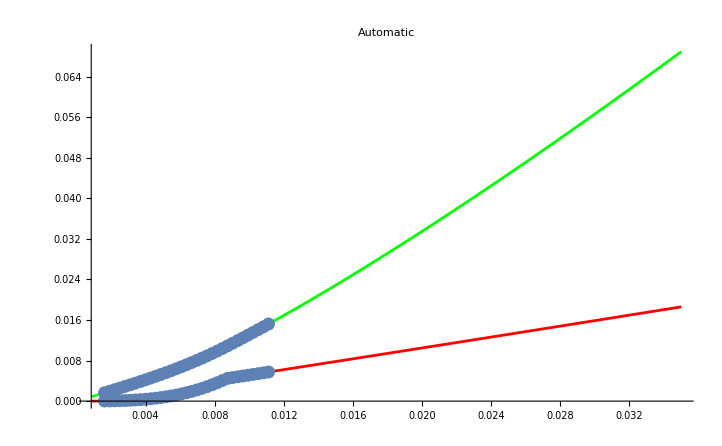

```mathematica
Plotlist={};
For[i=2,i<Length[narr]+1,i++,
(**AppendTo[Plotlist,Plot[μPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Blue]];
(**AppendTo[Plotlist,ListPlot[Transpose@{narr,μarr}]];**)
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,μEoSI}]];**)
AppendTo[Plotlist,Plot[PPP[n, Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Red]];
AppendTo[Plotlist,Plot[epsPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Green]];
(**AppendTo[Plotlist,Plot[1,{n,narr[[i-1]],narr[[i]]},PlotStyle->Black]];
AppendTo[Plotlist,Plot[csPP[n, carr[[i]], Γarr[[i]], Karr[[i]]],{n,narr[[i-1]],narr[[i]]},PlotStyle->Purple]];**)]
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,PEoSI}]];
AppendTo[Plotlist,ListPlot[Transpose@{nEoSI,ϵEoSI}]];
(**Show[Plotlist,PlotRange->{{0,0.004},{0,0.0001}},PlotLabel->Automatic]**)
Show[Plotlist,PlotRange->All,PlotLabel->Automatic]
```

```mathematica
convmN4=101425.86
```

101426.

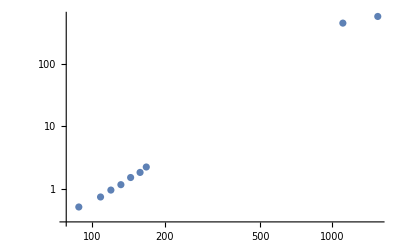

```mathematica
ListLogLogPlot[Table[{epsarr[[i]]*convmN4,Parr[[i]]*convmN4},{i,1,Length[Parr]}]]
```

```mathematica
epsarrout=epsarr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Parrout=Parr[[1;;9]]*convmN4 (** 1GeV^4 in MeV/fm^3**)
Export[NotebookDirectory[]<>"output/EoS_I_points.dat",{epsarrout,Parrout}]
```

{87.8368,108.178,119.456,131.49,144.348,158.021,167.728,1104.56,1543.56}

{0.510237,0.738351,0.953364,1.16388,1.51591,1.83,2.23549,455.871,582.845}

/home/dengler_yannick/Documents/new_neutron_star_plots/TOV_final/EoS_calc/output/EoS_I_points.dat